# using Framework to solve sparse optimization problem

This recompiles framework after changing f and df. Changing these does not require rebuilding the WSTP wrapper code (it does not explicitly know about these)

## Exporting the code

```mathematica
exportDefinitions[rif_]:=(
Print["rif: ",RIFunctionOutputExpressionMap[rif]];

Export["$CFormDefines.cpp",$CFormDefines,"Text"];
(*DEBUG globals lengthz, lengthfz for debugging*)
Export["lengthz.cpp",lengthz=RIFunctionArgumentsLength@rif,"Text"];
Export["lengthfz.cpp",lengthfz=RIFunctionOutputsLength@rif,"Text"];

Export["f.cpp",rif//RIFunctionCFormOutputArrayAssignments//ToCCodeString,"Text"];
Export["df.cpp",rif//RIFunctionCFormAllDerivativesIndexed//ToCCodeString,"Text"];
);
exportDefinitions@RIFunctionMakeFromExpressionList[{x},{x}];
exportDefinitions[f_,select_]:=With[{s0=select@Undefined},exportDefinitions@RIFunctionMakeFromExpressionList[f,Keys@s0]];

$FrameworkDirectory=NotebookDirectory[];
compile[]:=(TaskKill["Framework.exe"];SetDirectory@$FrameworkDirectory;Print@MSBuild["Framework.sln"])(*TODO rename and cache the exe based on the code*)

prepare[f_,select_]:=(
exportDefinitions[f,select];
compile[];
reload[])
```

After rebuilding, use reload[] to load stuff again

## Interfacing with the code

```mathematica
(*flattenSparseDerivativeZtoYIndices format*)
flattenZtoYIndicesOnce[i:{z:{___Integer},y:{___Integer}}]/;Length@z===Length@y:=Flatten@i~Prepend~Length@z;

flattenZtoYIndicesOnce[{{1,2,3},{4,5,6}}]~VerificationTest~{3,1,2,3,4,5,6}

flattenSparseDerivativeZtoYIndices[i:{{{___Integer},{___Integer}}?(AllEqual[Length])..}]:=Join@@(flattenZtoYIndicesOnce/@i);

(*one last test of the serialization format for sparseDerivativeZtoYIndices*)
reload[];
receiveAndPrintOptimizationData[1,1,(*lengthz, lengthfz*)
{1.,2.},(*x*)
flattenSparseDerivativeZtoYIndices@{{{0},{0}},{{0},{1}}},(*lengthP*)
Flatten[{{0},{0}}],(*xIndices lengthP*)
{0,1}(*yIndices*)
]
(*the console should display: (TODO: return this data and add a VerificationTest)
lengthz: 1
lengthfz: 1
lengthP: 2
lengthY: 2
lengthFx: 2
maxNNZ: 2
x:
1.000000 2.000000
sparseDerivativeZtoYIndices:
---
0
-->
0
---
---
0
-->
1
---
xIndices:
0
0
yIndices:
0 1
*)

Off[StringTrim::strse];(*CSwitch bug shut up*)

(*TODO split setup and solving into parts such that we can solve multiple times*)
optimize[select_,ps_,data_,ys_]:=Module[{val,xs,xIndices,yIndices,Global`sparseDerivativeZtoYIndices},
(*Derived data that is sent over*)
xs=Keys@data;
Global`sparseDerivativeZtoYIndices=SOP`SOPSparseDerivativeZtoYIndices[select,ps,ys];
xIndices=SOP`SOPxIndices[select,ps,xs];
yIndices=SOP`SOPyIndices[xs,ys];

(*parameters to the routines*)
val={
Values@data,
flattenSparseDerivativeZtoYIndices@(Global`sparseDerivativeZtoYIndices//CIndex),
Flatten@xIndices//CIndex,
yIndices//CIndex
};

(*for debugging, use this null routine*)
SOPCompiled`Private`receiveAndPrintOptimizationData[
lengthz,lengthfz,
Sequence@@val
];

(*actual work*)
receiveOptimizationDataBuildFxAndJFx[
Sequence@@val
];

(*solve[];-- done above*)
addContinuouslySmallerMultiplesOfHtoXUntilNorm2FxIsSmallerThanBefore[];
xGet[](*TODO doing just yGet would submit less data*)
];
```

TestResultObject[…]

## receiveOptimizationDataBuildFxAndJFx tests

Run these only when the correct code has been built.

They don’t query the current lengthz/lengthfz (it is not exposed) but it is displayed at startup

```mathematica
(*use only when compiled for lengthz=lengthfz=1*)
receiveOptimizationDataBuildFxAndJFx[
{3.},
flattenSparseDerivativeZtoYIndices@{{{0},{0}}},(*,{{0},{1}}*)
{0},
{0}](*output you see depends on current definition of f and df*)
```

```mathematica
(*for lengthz=lengthfz=2*)
receiveOptimizationData[
{1.,2.},
flattenSparseDerivativeZtoYIndices@{{{0,1},{0,1}}},(*,{{0},{1}}*)
{0,1},
{1,0}]
xGet[]~VerificationTest~{1.,2.}
getY[2]~VerificationTest~{2.,1.}
yIndicesGet[]~VerificationTest~{1,0}
```

TestResultObject[…]

TestResultObject[…]

TestResultObject[…]

```mathematica
(*for lengthz=lengthfz=2*)
receiveOptimizationDataBuildFxAndJFx[
{1.,2.},
flattenSparseDerivativeZtoYIndices@{{{0,1},{0,1}}},(*,{{0},{1}}*)
{0,1},
{0,1}]
```

```mathematica
(*for lengthz=lengthfz=2*)
receiveOptimizationDataBuildFxAndJFx[
{1.,2.},
flattenSparseDerivativeZtoYIndices@{
{{0,1},{0,1}},
{{0,1},{0,1}}
},(*,{{0},{1}}*)
Flatten@{
{0,1},
{0,1}
},
{0,1}]
```

```mathematica
(*for lengthz=lengthfz=2*)
receiveOptimizationDataBuildFxAndJFx[
{1.,2.},
flattenSparseDerivativeZtoYIndices@{
{{0,1},{1,0}}

},(*,{{0},{1}}*)
{0,1},
{0,1}]
```

## Example 1 - as tiny as it gets

```mathematica
ClearAll[x,select];

(*General Problem setup (size independent)*)
f={x};
select[i_]:={IdentityRule@x}

prepare[f,select]
```

Size dependent

```mathematica
ps={0}
data={x->2.}
ys={x};

optimize[select,ps,data,ys]~VerificationTest~{0.}(*the best solution is x=0.*)
```

{0}

{x→2.}

TestResultObject[…]

## Example 2

```mathematica
ClearAll[select,f,x,y];
f={2y,x+3y};
select[i_]:=IdentityRule/@{x,y}

prepare[f,select]
```

Size dependent

```mathematica
ys={x,y}
ps=Range[10]
data={x->2.,y->3.}

VerificationTest@ApproximatelyEqual[optimize[select,ps,data,ys],{0.,0.},10^-4](*solution is x = 0, y = 0*)
```

{x,y}

{1,2,3,4,5,6,7,8,9,10}

{x→2.,y→3.}

TestResultObject[…]

## Example 3 simple total variational smoothing

```mathematica
f={wsmooth,wdata}*{d[0]-d[-1],d[0]-d0[0]};
select[position_]:={
IdentityRule@wsmooth,
IdentityRule@wdata,
d[-1]->d[position-1],
d[0]->d[position],
d0[0]->d0[position]
};
prepare[f,select]
```

Size dependent

{d[1],d[2],d[3],d[4],d[5],d[6],d[7],d[8],d[9],d[10],d[11],d[12],d[13],d[14],d[15],d[16],d[17],d[18],d[19],d[20],d[21],d[22],d[23],d[24],d[25],d[26],d[27],d[28],d[29],d[30],d[31],d[32],d[33],d[34],d[35],d[36],d[37],d[38],d[39],d[40],d[41],d[42],d[43],d[44],d[45],d[46],d[47],d[48],d[49],d[50],d[51],d[52],d[53],d[54],d[55],d[56],d[57],d[58],d[59],d[60],d[61],d[62],d[63],d[64],d[65],d[66],d[67],d[68],d[69],d[70],d[71],d[72],d[73],d[74],d[75],d[76],d[77],d[78],d[79],d[80],d[81],d[82],d[83],d[84],d[85],d[86],d[87],d[88],d[89],d[90],d[91],d[92],d[93],d[94],d[95],d[96],d[97],d[98]}

{d[0],d[1],d[2],d[3],d[4],d[5],d[6],d[7],d[8],d[9],d[10],d[11],d[12],d[13],d[14],d[15],d[16],d[17],d[18],d[19],d[20],d[21],d[22],d[23],d[24],d[25],d[26],d[27],d[28],d[29],d[30],d[31],d[32],d[33],d[34],d[35],d[36],d[37],d[38],d[39],d[40],d[41],d[42],d[43],d[44],d[45],d[46],d[47],d[48],d[49],d[50],d[51],d[52],d[53],d[54],d[55],d[56],d[57],d[58],d[59],d[60],d[61],d[62],d[63],d[64],d[65],d[66],d[67],d[68],d[69],d[70],d[71],d[72],d[73],d[74],d[75],d[76],d[77],d[78],d[79],d[80],d[81],d[82],d[83],d[84],d[85],d[86],d[87],d[88],d[89],d[90],d[91],d[92],d[93],d[94],d[95],d[96],d[97],d[98],d[99],d0[1],d0[2],d0[3],d0[4],d0[5],d0[6],d0[7],d0[8],d0[9],d0[10],d0[11],d0[12],d0[13],d0[14],d0[15],d0[16],d0[17],d0[18],d0[19],d0[20],d0[21],d0[22],d0[23],d0[24],d0[25],d0[26],d0[27],d0[28],d0[29],d0[30],d0[31],d0[32],d0[33],d0[34],d0[35],d0[36],d0[37],d0[38],d0[39],d0[40],d0[41],d0[42],d0[43],d0[44],d0[45],d0[46],d0[47],d0[48],d0[49],d0[50],d0[51],d0[52],d0[53],d0[54],d0[55],d0[56],d0[57],d0[58],d0[59],d0[60],d0[61],d0[62],d0[63],d0[64],d0[65],d0[66],d0[67],d0[68],d0[69],d0[70],d0[71],d0[72],d0[73],d0[74],d0[75],d0[76],d0[77],d0[78],d0[79],d0[80],d0[81],d0[82],d0[83],d0[84],d0[85],d0[86],d0[87],d0[88],d0[89],d0[90],d0[91],d0[92],d0[93],d0[94],d0[95],d0[96],d0[97],d0[98],wsmooth,wdata}

{d[0]→0.12951,d[1]→0.880566,d[2]→0.48293,d[3]→0.381179,d[4]→0.379164,d[5]→0.126035,d[6]→0.153386,d[7]→0.732171,d[8]→0.863831,d[9]→0.124498,d[10]→0.269104,d[11]→0.272478,d[12]→0.361769,d[13]→0.11269,d[14]→0.943402,d[15]→0.413057,d[16]→0.598684,d[17]→0.393706,d[18]→0.534304,d[19]→0.989336,d[20]→0.0015572,d[21]→0.413668,d[22]→0.170764,d[23]→0.0674376,d[24]→0.274218,d[25]→0.72338,d[26]→0.737923,d[27]→0.773928,d[28]→0.259655,d[29]→0.0649873,d[30]→0.0710461,d[31]→0.677577,d[32]→0.956603,d[33]→0.870317,d[34]→0.717376,d[35]→0.262722,d[36]→0.0987194,d[37]→0.140194,d[38]→0.561934,d[39]→0.412185,d[40]→0.168112,d[41]→0.70368,d[42]→0.399871,d[43]→0.300317,d[44]→0.167786,d[45]→0.511665,d[46]→0.980694,d[47]→0.495405,d[48]→0.0189605,d[49]→0.958947,d[50]→0.946916,d[51]→0.459977,d[52]→0.205688,d[53]→0.385825,d[54]→0.181447,d[55]→0.0309554,d[56]→0.643522,d[57]→0.0306865,d[58]→0.573764,d[59]→0.628969,d[60]→0.416405,d[61]→0.777329,d[62]→0.895689,d[63]→0.994756,d[64]→0.398795,d[65]→0.102034,d[66]→0.232413,d[67]→0.694875,d[68]→0.00857815,d[69]→0.284719,d[70]→0.509874,d[71]→0.0904723,d[72]→0.0788802,d[73]→0.738109,d[74]→0.237593,d[75]→0.390968,d[76]→0.0226297,d[77]→0.293532,d[78]→0.604857,d[79]→0.863023,d[80]→0.692378,d[81]→0.689917,d[82]→0.330419,d[83]→0.788955,d[84]→0.189447,d[85]→0.727763,d[86]→0.619691,d[87]→0.39239,d[88]→0.814801,d[89]→0.660573,d[90]→0.835904,d[91]→0.503521,d[92]→0.779176,d[93]→0.620455,d[94]→0.587883,d[95]→0.829279,d[96]→0.143213,d[97]→0.733288,d[98]→0.865914,d[99]→0.0414676,d0[1]→0.236222,d0[2]→0.249636,d0[3]→0.958152,d0[4]→0.990075,d0[5]→0.972355,d0[6]→0.946573,d0[7]→0.0584297,d0[8]→0.88954,d0[9]→0.771519,d0[10]→0.512788,d0[11]→0.266739,d0[12]→0.211468,d0[13]→0.738415,d0[14]→0.209923,d0[15]→0.208302,d0[16]→0.730756,d0[17]→0.572779,d0[18]→0.854689,d0[19]→0.687115,d0[20]→0.189698,d0[21]→0.558472,d0[22]→0.0881328,d0[23]→0.397984,d0[24]→0.377201,d0[25]→0.888485,d0[26]→0.210478,d0[27]→0.320365,d0[28]→0.0668006,d0[29]→0.311262,d0[30]→0.760087,d0[31]→0.162396,d0[32]→0.325786,d0[33]→0.234982,d0[34]→0.851357,d0[35]→0.323474,d0[36]→0.614143,d0[37]→0.555528,d0[38]→0.576501,d0[39]→0.722333,d0[40]→0.378967,d0[41]→0.199313,d0[42]→0.834936,d0[43]→0.297991,d0[44]→0.951626,d0[45]→0.938527,d0[46]→0.873267,d0[47]→0.114079,d0[48]→0.0822867,d0[49]→0.0346704,d0[50]→0.849334,d0[51]→0.607869,d0[52]→0.451211,d0[53]→0.761364,d0[54]→0.690608,d0[55]→0.487543,d0[56]→0.733353,d0[57]→0.656922,d0[58]→0.469463,d0[59]→0.240932,d0[60]→0.56386,d0[61]→0.825941,d0[62]→0.146283,d0[63]→0.732799,d0[64]→0.325089,d0[65]→0.379169,d0[66]→0.823965,d0[67]→0.902247,d0[68]→0.406724,d0[69]→0.110833,d0[70]→0.92639,d0[71]→0.386011,d0[72]→0.652829,d0[73]→0.32378,d0[74]→0.773629,d0[75]→0.990992,d0[76]→0.555202,d0[77]→0.442725,d0[78]→0.274867,d0[79]→0.16843,d0[80]→0.0433451,d0[81]→0.567378,d0[82]→0.267634,d0[83]→0.00138624,d0[84]→0.675207,d0[85]→0.808422,d0[86]→0.931184,d0[87]→0.664997,d0[88]→0.845581,d0[89]→0.799616,d0[90]→0.388872,d0[91]→0.898276,d0[92]→0.705139,d0[93]→0.945367,d0[94]→0.0539372,d0[95]→0.325757,d0[96]→0.612972,d0[97]→0.457013,d0[98]→0.555643,wsmooth→1.,wdata→1.}

{0.12951,0.262087,0.420529,0.749864,0.870912,0.872795,0.775118,0.505987,0.684412,0.657709,0.517195,0.381087,0.359326,0.485422,0.358527,0.380236,0.57388,0.610648,0.685285,0.590518,0.399155,0.417249,0.29412,0.376979,0.438833,0.56232,0.359642,0.306127,0.238375,0.342198,0.476955,0.328583,0.346398,0.384825,0.573095,0.483103,0.552741,0.560976,0.57466,0.586502,0.462515,0.422076,0.6044,0.556187,0.76617,0.790699,0.667399,0.338231,0.233214,0.279125,0.569489,0.580009,0.562671,0.656792,0.646343,0.591629,0.641,0.59802,0.496138,0.420932,0.525726,0.592386,0.425492,0.537808,0.455132,0.5025,0.673197,0.693126,0.503933,0.411951,0.621086,0.524916,0.567652,0.525212,0.684204,0.753771,0.586117,0.449377,0.319288,0.23362,0.213143,0.362464,0.306871,0.290515,0.563288,0.724141,0.800713,0.746815,0.774735,0.731808,0.621075,0.742544,0.708281,0.677158,0.377828,0.402386,0.503574,0.495363,0.525503,0.0414676,0.236222,0.249636,0.958152,0.990075,0.972355,0.946573,0.0584297,0.88954,0.771519,0.512788,0.266739,0.211468,0.738415,0.209923,0.208302,0.730756,0.572779,0.854689,0.687115,0.189698,0.558472,0.0881328,0.397983,0.377201,0.888485,0.210478,0.320365,0.0668006,0.311262,0.760087,0.162396,0.325787,0.234982,0.851357,0.323474,0.614143,0.555528,0.576501,0.722333,0.378967,0.199313,0.834936,0.297991,0.951626,0.938527,0.873267,0.114079,0.0822866,0.0346704,0.849334,0.607869,0.451211,0.761364,0.690608,0.487543,0.733353,0.656922,0.469463,0.240932,0.56386,0.825941,0.146283,0.732799,0.325089,0.379169,0.823965,0.902247,0.406724,0.110833,0.92639,0.386011,0.652829,0.32378,0.773629,0.990992,0.555202,0.442725,0.274867,0.16843,0.0433451,0.567378,0.267634,0.00138624,0.675207,0.808422,0.931184,0.664997,0.845581,0.799616,0.388872,0.898276,0.705139,0.945367,0.0539372,0.325757,0.612972,0.457013,0.555643,1.,1.}

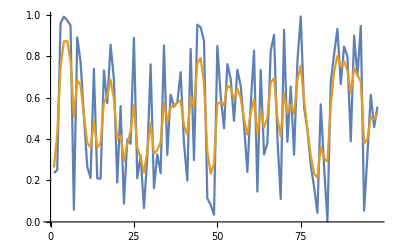

```mathematica
n=100;
ys=Array[d,n-2,1]

xs=Array[d,n,0]~Join~Array[d0,n-2,1]~Join~{wsmooth,wdata}

data=Thread@Rule[xs,RandomReal[1.,Length@xs-2]~Join~{1.,1.}]
ps=Array[Identity,n-2,1];

sol=optimize[select,ps,data,ys]

ListLinePlot[{
Take[Values@data,{n+1,n+1+n-3}],
Take[sol,{2,n-1}]
}]
```

verifying the LeastSquares implementation

```mathematica
LeastSquares[{{1,1,-1,0},{0,0,1,1}}//Transpose,Flatten["0.098247 -0.310309 0.409989 0.392858"~ImportString~"Table"]]
```

{-0.088251,0.357298}